```mathematica
kellycols=RGBColor/@({{230,25,75},{60,180,75},(*{255,225,25},*){0,130,200},{245,130,48},{145,30,180},{70,240,240},{240,50,230},{210,245,60},{250,190,212},{0,128,128},{220,190,255},{170,110,40},{255,250,200},{128,0,0},{170,255,195},{128,128,0},{255,215,180},{0,0,128},{128,128,128},{255,255,255},{0,0,0}}/255)
```

{RGBColor[{Rational[46, 51], Rational[5, 51], Rational[5, 17]}],RGBColor[{Rational[4, 17], Rational[12, 17], Rational[5, 17]}],RGBColor[{0, Rational[26, 51], Rational[40, 51]}],RGBColor[{Rational[49, 51], Rational[26, 51], Rational[16, 85]}],RGBColor[{Rational[29, 51], Rational[2, 17], Rational[12, 17]}],RGBColor[{Rational[14, 51], Rational[16, 17], Rational[16, 17]}],RGBColor[{Rational[16, 17], Rational[10, 51], Rational[46, 51]}],RGBColor[{Rational[14, 17], Rational[49, 51], Rational[4, 17]}],RGBColor[{Rational[50, 51], Rational[38, 51], Rational[212, 255]}],RGBColor[{0, Rational[128, 255], Rational[128, 255]}],RGBColor[{Rational[44, 51], Rational[38, 51], 1}],RGBColor[{Rational[2, 3], Rational[22, 51], Rational[8, 51]}],RGBColor[{1, Rational[50, 51], Rational[40, 51]}],RGBColor[{Rational[128, 255], 0, 0}],RGBColor[{Rational[2, 3], 1, Rational[13, 17]}],RGBColor[{Rational[128, 255], Rational[128, 255], 0}],RGBColor[{1, Rational[43, 51], Rational[12, 17]}],RGBColor[{0, 0, Rational[128, 255]}],RGBColor[{Rational[128, 255], Rational[128, 255], Rational[128, 255]}],RGBColor[{1, 1, 1}],RGBColor[{0, 0, 0}]}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"line_points.csv"}],Table[{6,μ},{μ,-0.15,0.1,0.25/400}]]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass 5\line_points.csv

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"line_points2.csv"}],Table[{β,-2},{β,0.1,1.1,1./400}]]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass 5\line_points2.csv

```mathematica
data1={#1[[2]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"line_points.csv"}]],Abs@Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_200_4096_line_points.csv"}]]}];
```

```mathematica
negfitdata1=Select[data1,#[[1]]<=-0.03&];
posfitdata1=Select[data1,#[[1]]>=0.003&];
```

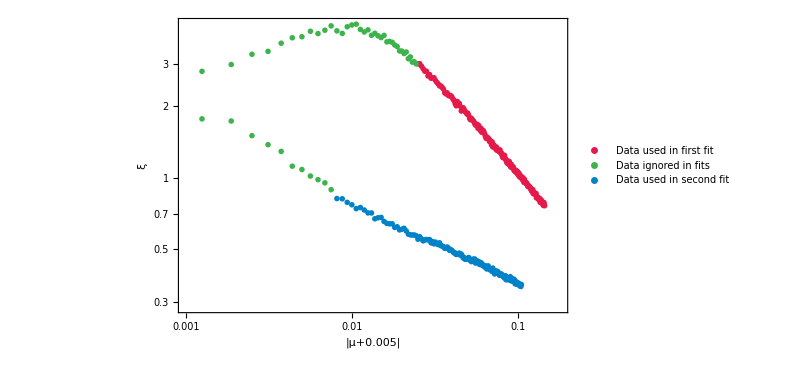

```mathematica
llp1=ListLogLogPlot[{{Abs[#1+0.005],#2}&@@@negfitdata1,{Abs[#1+0.005],#2}&@@@Complement[data1,negfitdata1,posfitdata1],{Abs[#1+0.005],#2}&@@@posfitdata1},Frame->True,PlotStyle->Take[kellycols,3],Axes->False,PlotMarkers->{"OpenMarkers",Small},FrameLabel->{{"ξ",""},{"|μ+0.005|","β=6"}},LabelStyle->Directive[Bold, 14],PlotLegends->{"Data used in first fit","Data ignored in fits","Data used in second fit"},PlotRange->{{0.001,0.18},All},ImageSize->600]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","llp1.png"}],llp1]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass 5\Report\figures\llp1.png

```mathematica
nlmL=NonlinearModelFit[negfitdata1,a/Abs[b+x]^c,{a,{b,0.},c},x,MaxIterations->10000]
nlmR=NonlinearModelFit[posfitdata1,a/Abs[b+x]^c,{a,{b,0.},c},x,MaxIterations->10000]
```

FittedModel[0.136848/Abs[-0.00401739+x]^0.915605]

FittedModel[0.171877/Abs[0.00488872+x]^0.323269]

```mathematica
nlmL["BestFitParameters"]
nlmR["BestFitParameters"]
```

{a→0.136848,b→-0.00401739,c→0.915605}

{a→0.171877,b→0.00488872,c→0.323269}

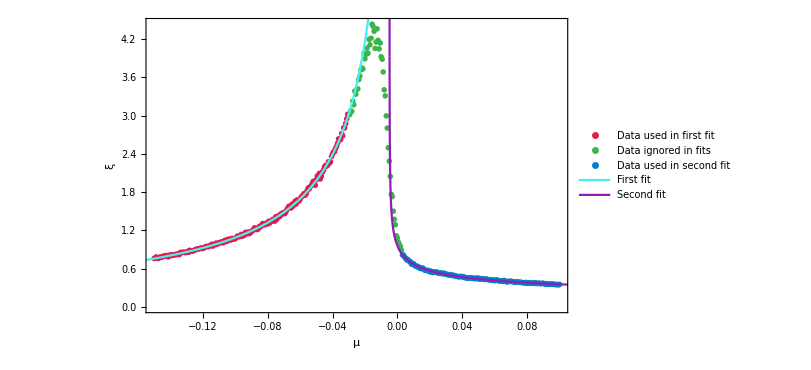

```mathematica
fp1=Show[ListPlot[{negfitdata1,Complement[data1,negfitdata1,posfitdata1],posfitdata1},Frame->True,PlotStyle->Take[kellycols,3],Axes->False,PlotMarkers->{"OpenMarkers",Small},FrameLabel->{{"ξ",""},{"μ","β=6"}},LabelStyle->Directive[Bold, 14],PlotLegends->{"Data used in first fit","Data ignored in fits","Data used in second fit"}],Plot[nlmL[x],{x,-0.2,0},PlotStyle->kellycols[[6]],PlotLegends->{"First fit"},LabelStyle->Directive[Bold, 14]],Plot[nlmR[x],{x,-b/.nlmR["BestFitParameters"],0.2},PlotStyle->kellycols[[5]],PlotRange->All,PlotLegends->{"Second fit"},LabelStyle->Directive[Bold, 14]],ImageSize->600]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","fp1.png"}],fp1]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass 5\Report\figures\fp1.png

```mathematica
data2={#1[[1]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"line_points2.csv"}]],Abs@Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_200_4096_line_points2.csv"}]]}];
```

```mathematica
negfitdata2=Select[data2,0.22<=#[[1]]<=0.427&];
posfitdata2=Select[data2,#[[1]]>=0.485&];
```

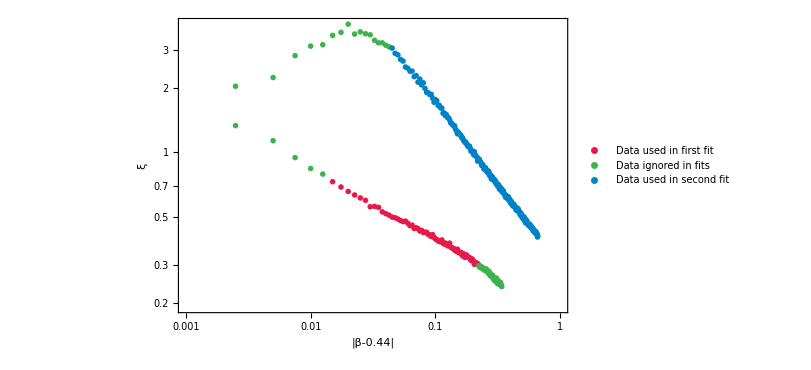

```mathematica
llp2=ListLogLogPlot[{{Abs[#1-0.44],#2}&@@@negfitdata2,{Abs[#1-0.44],#2}&@@@Complement[data2,negfitdata2,posfitdata2],{Abs[#1-0.44],#2}&@@@posfitdata2},Frame->True,PlotStyle->Take[kellycols,3],Axes->False,PlotMarkers->{"OpenMarkers",Small},FrameLabel->{{"ξ",""},{"|β-0.44|","μ=-2"}},LabelStyle->Directive[Bold, 14],PlotLegends->{"Data used in first fit","Data ignored in fits","Data used in second fit"},PlotRange->{{0.001,1},All},ImageSize->600]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","llp2.png"}],llp2]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass 5\Report\figures\llp2.png

```mathematica
nlmL2=NonlinearModelFit[negfitdata2,a/Abs[x-b]^c,{a,{b,0.45},c},x,MaxIterations->10000]
nlmR2=NonlinearModelFit[posfitdata2,a/Abs[x+b]^c,{a,{b,0.41},c},x,MaxIterations->10000]
```

FittedModel[0.19061/Abs[-0.439722+x]^0.315848]

FittedModel[0.290835/Abs[-0.434053+x]^0.788524]

```mathematica
nlmL2["BestFitParameters"]
nlmR2["BestFitParameters"]
```

{a→0.19061,b→0.439722,c→0.315848}

{a→0.290835,b→-0.434053,c→0.788524}

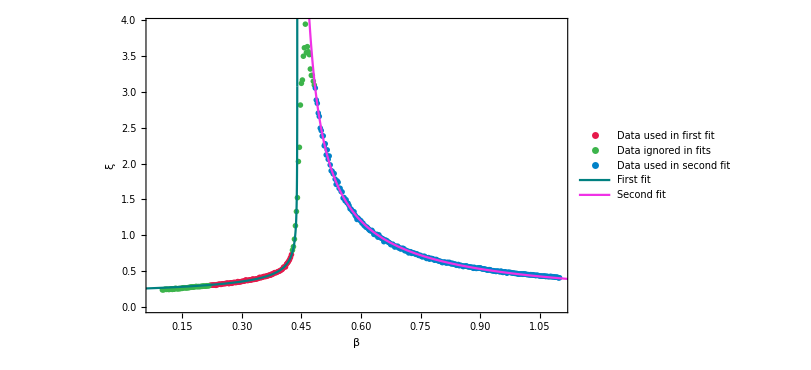

```mathematica
fp2=Show[ListPlot[{negfitdata2,Complement[data2,negfitdata2,posfitdata2],posfitdata2},Frame->True,PlotStyle->Take[kellycols,3],Axes->False,PlotMarkers->{"OpenMarkers",Small},FrameLabel->{{"ξ",""},{"β","μ=-2"}},LabelStyle->Directive[Bold, 14],PlotLegends->{"Data used in first fit","Data ignored in fits","Data used in second fit"},PlotRange->All],Plot[nlmL2[x],{x,0,b/.nlmL2["BestFitParameters"]},PlotStyle->kellycols[[10]],PlotLegends->{"First fit"},LabelStyle->Directive[Bold, 14],PlotRange->All],Plot[nlmR2[x],{x,-b/.nlmR2["BestFitParameters"],1.5},PlotStyle->kellycols[[7]],PlotRange->All,PlotLegends->{"Second fit"},LabelStyle->Directive[Bold, 14]],ImageSize->600]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","fp2.png"}],fp2]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass 5\Report\figures\fp2.png

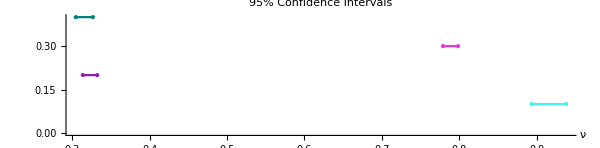

```mathematica
nlp1=NumberLinePlot[{Interval[Last@nlmL["ParameterConfidenceIntervals"]],Interval[Last@nlmR["ParameterConfidenceIntervals"]],Interval[Last@nlmR2["ParameterConfidenceIntervals"]],Interval[Last@nlmL2["ParameterConfidenceIntervals"]]},PlotStyle->{kellycols[[6]],kellycols[[5]],kellycols[[7]],kellycols[[10]]},PlotLegends->(Style[#,Bold,16,FontFamily->"Times"]&/@{"ν_β","ν_β'","ν_μ","ν_μ'"}),LabelStyle->Directive[Bold, 14],AxesLabel->{Style["ν",Bold,18,FontFamily->"Times"],""},PlotLabel->"95% Confidence Intervals",ImageSize->600,Spacings->0.1]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","nlp1.png"}],nlp1]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass 5\Report\figures\nlp1.png

## All

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"points.csv"}],Flatten[Table[{β,μ},{β,-15.,15.,30./100},{μ,-2.,3.,5./100}],1]]
Export[FileNameJoin[{NotebookDirectory[],"points2.csv"}],Flatten[Table[{β,μ},{β,-15.,15.,30./200},{μ,-2.,3.,5./200}],1]]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass 5\points.csv

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass 5\points2.csv

```mathematica
ldp=ListDensityPlot[{#1[[2]],#1[[1]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"points2.csv"}]],Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_100_256_points2.csv"}]]}],ColorFunction->"SunsetColors",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{5,5}},LegendLabel->"ξ",LabelStyle->{Directive[Bold, 14]}],Above],ImageSize->400,LabelStyle->Directive[Bold, 14],FrameLabel->{"μ","β"}]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","ldp.png"}],ldp]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass 5\Report\figures\ldp.png

## Diagonal

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"line_points3.csv"}],Table[{-4μ,μ},{μ,-1.1,1.75,3.5/800}]]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass 5\line_points3.csv

```mathematica
data3={#1[[2]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"line_points3.csv"}]],Abs@Flatten@Import[FileNameJoin[{NotebookDirectory[],"out_200_2048_line_points3.csv"}]]}];
```

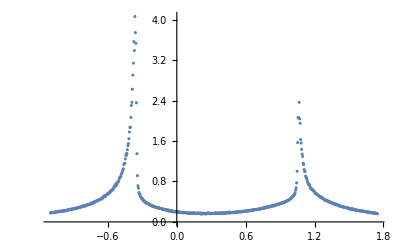

```mathematica
ListPlot[data3,PlotRange->All]
```

```mathematica
fd1=Select[data3,-0.8<=#[[1]]<=-0.38&];
fd2=Select[data3,-0.34<=#[[1]]<=-0.22&];
fd3=Select[data3,0.915<=#[[1]]<=1.04&];
fd4=Select[data3,1.1<=#[[1]]<=1.5&];
```

```mathematica
llp3=GraphicsRow[{ListLogLogPlot[{{Abs[#1+0.35],#2}&@@@fd1,{Abs[#1+0.35],#2}&@@@Complement[data3,fd1,fd2],{Abs[#1+0.35],#2}&@@@fd2},Frame->True,PlotStyle->Take[kellycols,3],Axes->False,PlotMarkers->{"OpenMarkers",Small},FrameLabel->{{"ξ",""},{"|μ+0.35|","β=-4μ"}},LabelStyle->Directive[Bold, 10],PlotLegends->{"Data used in first fit","Other Data","Data used in second fit"},PlotRange->{{0.01,2},All},ImageSize->400],
ListLogLogPlot[{{Abs[#1-1.05],#2}&@@@fd3,{Abs[#1-1.05],#2}&@@@Complement[data3,fd3,fd4],{Abs[#1-1.05],#2}&@@@fd4},Frame->True,PlotStyle->Take[kellycols,3],Axes->False,PlotMarkers->{"OpenMarkers",Small},FrameLabel->{{"ξ",""},{"|μ-1.05|","β=-4μ"}},LabelStyle->Directive[Bold, 10],PlotLegends->{"Data used in third fit","Other Data","Data used in fourth fit"},PlotRange->{{0.01,2},All},ImageSize->400]},ImageSize->1200]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","llp3.png"}],llp3]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass 5\Report\figures\llp3.png

```mathematica
nlm1=NonlinearModelFit[fd1,a/Abs[x-b]^c,{a,{b,0.4},c},x,MaxIterations->10000]
nlm2=NonlinearModelFit[fd2,a/Abs[x+b]^c,{a,{b,0.4},c},x,MaxIterations->10000]
nlm3=NonlinearModelFit[fd3,a/Abs[x-b]^c,{a,{b,1.1},c},x,MaxIterations->10000]
nlm4=NonlinearModelFit[fd4,a/Abs[x+b]^c,{a,{b,1.1},c},x,MaxIterations->10000]
```

FittedModel[0.163199/Abs[0.341308+x]^0.899508]

FittedModel[0.17136/Abs[0.350083+x]^0.319846]

FittedModel[0.240378/Abs[-1.05014+x]^0.226774]

FittedModel[0.16695/Abs[-1.04369+x]^0.67467]

```mathematica
nlm1["BestFitParameters"]
nlm2["BestFitParameters"]
nlm3["BestFitParameters"]
nlm4["BestFitParameters"]
```

{a→0.163199,b→-0.341308,c→0.899508}

{a→0.17136,b→0.350083,c→0.319846}

{a→0.240378,b→1.05014,c→0.226774}

{a→0.16695,b→-1.04369,c→0.67467}

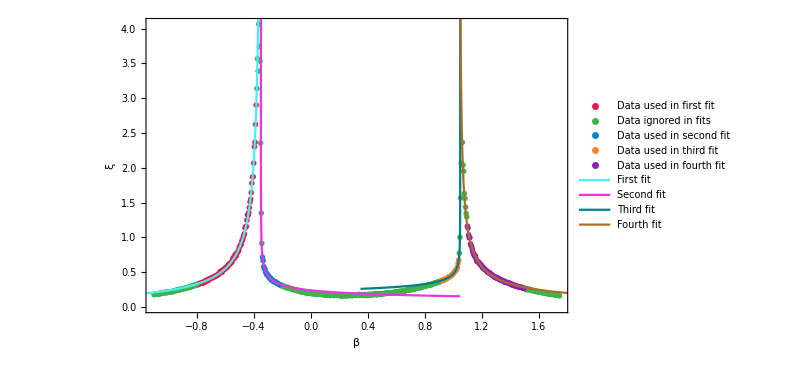

```mathematica
fp3=Show[ListPlot[{fd1,Complement[data3,fd1,fd2,fd3,fd4],fd2,fd3,fd4},Frame->True,PlotStyle->Take[kellycols,5],Axes->False,PlotMarkers->{"OpenMarkers",Small},FrameLabel->{{"ξ",""},{"β","μ=-2"}},LabelStyle->Directive[Bold, 14],PlotLegends->{"Data used in first fit","Data ignored in fits","Data used in second fit","Data used in third fit","Data used in fourth fit"},PlotRange->All],Plot[nlm1[x],{x,-1.5,b/.nlm1["BestFitParameters"]},PlotStyle->kellycols[[6]],PlotLegends->{"First fit"},LabelStyle->Directive[Bold, 14],PlotRange->All],Plot[nlm2[x],{x,-b/.nlm2["BestFitParameters"],b/.nlm3["BestFitParameters"]},PlotStyle->kellycols[[7]],PlotRange->All,PlotLegends->{"Second fit"},LabelStyle->Directive[Bold, 14]],Plot[nlm3[x],{x,b/.nlm2["BestFitParameters"],b/.nlm3["BestFitParameters"]},PlotStyle->kellycols[[10]],PlotLegends->{"Third fit"},LabelStyle->Directive[Bold, 14],PlotRange->All],Plot[nlm4[x],{x,-b/.nlm4["BestFitParameters"],2},PlotStyle->kellycols[[12]],PlotLegends->{"Fourth fit"},LabelStyle->Directive[Bold, 14],PlotRange->All],ImageSize->600]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","fp3.png"}],fp3]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass 5\Report\figures\fp3.png

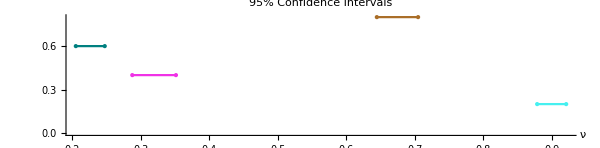

```mathematica
nlp2=NumberLinePlot[{Interval[Last@nlm1["ParameterConfidenceIntervals"]],Interval[Last@nlm2["ParameterConfidenceIntervals"]],Interval[Last@nlm3["ParameterConfidenceIntervals"]],Interval[Last@nlm4["ParameterConfidenceIntervals"]]},PlotStyle->{kellycols[[6]],kellycols[[7]],kellycols[[10]],kellycols[[12]]},PlotLegends->(Style[#,Bold,16,FontFamily->"Times"]&/@{"ν_1","ν_1'","ν_2'","ν_2"}),LabelStyle->Directive[Bold, 14],AxesLabel->{Style["ν",Bold,18,FontFamily->"Times"],""},PlotLabel->"95% Confidence Intervals",ImageSize->600,Spacings->0.2]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","nlp2.png"}],nlp2]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass 5\Report\figures\nlp2.png